3

4/3

3

19/6

-1/3

2/3

4/3

1/6

{{19/6,-1/3,-1/3,-1/3,-1/3,2/3,4/3,-1/6,4/3},{-1/3,19/6,-1/3,-1/3,2/3,-1/3,4/3,4/3,-1/6},{-1/3,-1/3,19/6,2/3,-1/3,-1/3,-1/6,4/3,4/3},{-1/3,-1/3,2/3,19/6,-1/3,-1/3,-1/6,4/3,4/3},{-1/3,2/3,-1/3,-1/3,19/6,-1/3,4/3,4/3,-1/6},{2/3,-1/3,-1/3,-1/3,-1/3,19/6,4/3,-1/6,4/3},{4/3,4/3,-1/6,-1/6,4/3,4/3,2/9,1/36,1/36},{-1/6,4/3,4/3,4/3,4/3,-1/6,1/36,2/9,1/36},{4/3,-1/6,4/3,4/3,-1/6,4/3,1/36,1/36,2/9}}

{{-3/2,0,0,0,0,0,0,0,-1/2},{0,-3/2,0,0,0,0,0,-1/2,0},{0,0,0,0,0,0,0,1/2,1/2},{0,0,0,0,0,0,0,1/2,1/2},{0,0,0,0,-3/2,0,0,-1/2,0},{0,0,0,0,0,-3/2,0,0,-1/2},{-1/2,-1/2,0,0,-1/2,-1/2,-3,0,0},{0,0,1/2,1/2,0,0,0,0,0},{0,0,1/2,1/2,0,0,0,0,0}}

{{0,0,0,0,0,0,1/2,0,1/2},{0,-3/2,0,0,0,0,-1/2,0,0},{0,0,-3/2,0,0,0,0,0,-1/2},{0,0,0,-3/2,0,0,0,0,-1/2},{0,0,0,0,-3/2,0,-1/2,0,0},{0,0,0,0,0,0,1/2,0,1/2},{1/2,0,0,0,0,1/2,0,0,0},{0,-1/2,-1/2,-1/2,-1/2,0,0,-3,0},{1/2,0,0,0,0,1/2,0,0,0}}

{{-3/2,0,0,0,0,0,-1/2,0,0},{0,0,0,0,0,0,1/2,1/2,0},{0,0,-3/2,0,0,0,0,-1/2,0},{0,0,0,-3/2,0,0,0,-1/2,0},{0,0,0,0,0,0,1/2,1/2,0},{0,0,0,0,0,-3/2,-1/2,0,0},{0,1/2,0,0,1/2,0,0,0,0},{0,1/2,0,0,1/2,0,0,0,0},{-1/2,0,-1/2,-1/2,0,-1/2,0,0,-3}}

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}

2

1

1

1

«1 more identical outputs»

2

-1

0

5

3

4/3

1/2

25/9+3 (-67/18+π^2/6)

-101/54+(11 π^2)/144+5/2 (14/27-π^2/36)+(7 Zeta[3])/4

23/3

116/3

-Log[2]

0

0

1

0

0

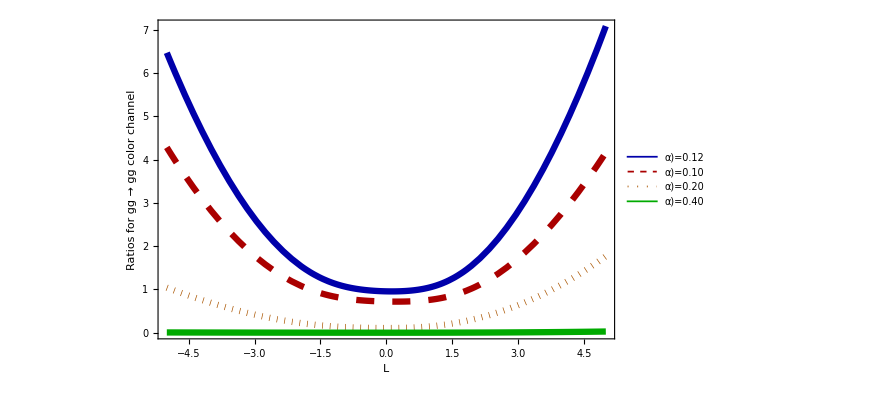

gg_to_gg_NLL_NNLL.png

```mathematica
Nc = 3
Cf = (Nc^2-1)/(2Nc)
CA = 3
a = Cf/(8 CA)*(CA^4-3CA^2 + 3)
b = Cf/(8 CA)*(3-CA^2)
c= Cf/(8 CA)*(3+CA^2)
d = Cf/(8 CA)*(2CA^2)*Cf
e = Cf/(8 CA)*(CA)
Tree=({{a, b, b, b, b, c, d, -e, d}, {b, a, b, b, c, b, d, d, -e}, {b, b, a, c, b, b, -e, d, d}, {b, b, c, a, b, b, -e, d, d}, {b, c, b, b, a, b, d, d, -e}, {c, b, b, b, b, a, d, -e, d}, {d, d, -e, -e, d, d, d*e, e^2, e^2}, {-e, d, d, d, d, -e, e^2, d*e, e^2}, {d, -e, d, d, -e, d, e^2, e^2, d*e}})
T12= ({{-3/2, 0, 0, 0, 0, 0, 0, 0, -1/2}, {0, -3/2, 0, 0, 0, 0, 0, -1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 1/2, 1/2}, {0, 0, 0, 0, 0, 0, 0, 1/2, 1/2}, {0, 0, 0, 0, -3/2, 0, 0, -1/2, 0}, {0, 0, 0, 0, 0, -3/2, 0, 0, -1/2}, {-1/2, -1/2, 0, 0, -1/2, -1/2, -3, 0, 0}, {0, 0, 1/2, 1/2, 0, 0, 0, 0, 0}, {0, 0, 1/2, 1/2, 0, 0, 0, 0, 0}})
T13 =({{0, 0, 0, 0, 0, 0, 1/2, 0, 1/2}, {0, -CA/2, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, -CA/2, 0, 0, 0, 0, 0, -1/2}, {0, 0, 0, -CA/2, 0, 0, 0, 0, -1/2}, {0, 0, 0, 0, -CA/2, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 1/2, 0, 1/2}, {1/2, 0, 0, 0, 0, 1/2, 0, 0, 0}, {0, -1/2, -1/2, -1/2, -1/2, 0, 0, -CA, 0}, {1/2, 0, 0, 0, 0, 1/2, 0, 0, 0}})
T23 =({{-CA/2, 0, 0, 0, 0, 0, -1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 1/2, 1/2, 0}, {0, 0, -CA/2, 0, 0, 0, 0, -1/2, 0}, {0, 0, 0, -CA/2, 0, 0, 0, -1/2, 0}, {0, 0, 0, 0, 0, 0, 1/2, 1/2, 0}, {0, 0, 0, 0, 0, -CA/2, -1/2, 0, 0}, {0, 1/2, 0, 0, 1/2, 0, 0, 0, 0}, {0, 1/2, 0, 0, 1/2, 0, 0, 0, 0}, {-1/2, 0, -1/2, -1/2, 0, -1/2, 0, 0, -CA}})
Unit = ({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}})
n12 = 2
n13 = 1
n23 = 1
n14 = 1
n24 = 1
n34 = 2
γ0Cusp = -1 
γ0 = 0
NF = 5
CA = 3
CF = 4/3
TR = 1/2
γ1Cusp = (π^2/6 - 67/18)*CA + (10/9)*NF*TR
γ1 = (11π^2/144  + 7Zeta[3]/4 - 101/54) + NF*TR*(14/27 - π^2/36)
β0 = (11/3)*CA - (4/3)*TR*NF
β1 = (34/3)*CA^2-4*CF*TR*NF- (20/3)*CA*TR*NF
l12 = Log[√((n14*n24)/(2*n12))] 
l13 = Log[√((n14*n34)/(2*n13))]
l23 = Log[√((n24*n34)/(2*n23))]
L12[L_]:= L +  Log[√((n14*n24)/(2*n12))] 
L13[L_]:= L +  Log[√((n14*n34)/(2*n13))]
 L23[L_]:= L +  Log[√((n24*n34)/(2*n23))]
 L1212[L_]:= L +  Log[√((n14*n24)/(2*n12))]
 L1213[L_]:= L + (1/2)* Log[√((n14*n24)/(2*n12))]+(1/2)* Log[√((n14*n34)/(2*n13))]
 L1223[L_]:= L + (1/2)* Log[√((n14*n24)/(2*n12))]+(1/2)* Log[√((n24*n34)/(2*n23))]
 L1312[L_]:= L1213[L]
L1313[L_]:= L +  Log[√((n14*n34)/(2*n13))]
L1323[L_]:= L + (1/2)* Log[√((n14*n34)/(2*n13))]+(1/2)* Log[√((n24*n34)/(2*n23))]
L2312[L_]:=  L1223[L]
L2313[L_]:=  L1323[L]
L2323[L_]:= L +  Log[√((n24*n34)/(2*n23))]
NLORenormalized[L_,αS_]:=(αS (-π^2/4))/(2 π)*2*(T12 + T13 + T23)+2*αS/(2 π)*((-2 L12[L]^2)*T12 + (-2 L23[L]^2)*T23 + (-2 L13[L]^2)*T13)
NNLORenormalized1[L_,αS_]:=2*(NF TR αS^2( 82/81+(25 π^2)/108+Zeta[3]/9))/(4 π^2)*(T12 + T13 + T23) + 2*(NF TR αS^2 ((56/27+(5 π^2)/9) L12[L]+20/9 L12[L]^2+16/9 L12[L]^3))/(4 π^2)*T12 +  2*(NF TR αS^2 ((56/27+(5 π^2)/9) L13[L]+20/9 L13[L]^2+16/9 L13[L]^3))/(4 π^2)*T13  +  2*(NF TR αS^2 ((56/27+(5 π^2)/9) L23[L]+20/9 L23[L]^2+16/9 L23[L]^3))/(4 π^2)*T23
NNLORenormalized2[L_,αS_]:=2*(αS^2 β0 (Zeta[3]/6))/(4 π^2)*(T12 + T13 + T23) + 2*(αS^2 β0 (1/4 π^2 L12[L]+2/3 L12[L]^3))/(4 π^2)*T12 + 2*(αS^2 β0 (1/4 π^2 L13[L]+2/3 L13[L]^3))/(4 π^2)*T13 + 2*(αS^2 β0 (1/4 π^2 L23[L]+2/3 L23[L]^3))/(4 π^2)*T23
NNLORenormalized3[L_,αS_]:=2*(CA αS^2 (-607/162-(335 π^2)/432+(7 π^4)/60-(11 Zeta[3])/36))/(4 π^2)*(T12 + T13 + T23) +2* (CA αS^2 ((-67/9+π^2/3) L12[L]^2-44/9 L12[L]^3+L12[L] (-202/27-(55 π^2)/36+7 Zeta[3])))/(4 π^2)*T12+2* (CA αS^2 ((-67/9+π^2/3) L13[L]^2-44/9 L13[L]^3+L13[L] (-202/27-(55 π^2)/36+7 Zeta[3])))/(4 π^2)*T13 + 2* (CA αS^2 ((-67/9+π^2/3) L23[L]^2-44/9 L23[L]^3+L23[L] (-202/27-(55 π^2)/36+7 Zeta[3])))/(4 π^2)*T23
NNLORenormalized4[L_,αS_]:=(αS^2 ((17 π^2)/480))/(4 π^2)*2*2*2*(T12 + T13 + T23).(T12 + T13 + T23)
NNLORenormalized5[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12.T12* L1212[L] + T12.T13* L1213[L] + T12.T23* L2323[L] + T13.T13* L1313[L] + T13.T23* L1323[L] +T13.T12* L1213[L] + T23.T12* L1223[L] +T23.T13* L1323[L] +T23.T23* L2323[L] )*(2Zeta[3]/3)
NNLORenormalized6[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12.T12* (L1212[L])^2 + T12.T13* (L1213[L])^2 + T12.T23* (L2323[L])^2 + T13.T13* (L1313[L])^2 + T13.T23* (L1323[L])^2 +T13.T12* (L1213[L])^2 + T23.T12* (L1223[L])^2 +T23.T13* (L1323[L])^2 +T23.T23* (L2323[L])^2 )*(π^2)
NNLORenormalized7[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12.T12* (L1212[L])^4 + T12.T13* (L1213[L])^4 + T12.T23* (L2323[L])^4 + T13.T13* (L1313[L])^4+ T13.T23* (L1323[L])^4 +T13.T12* (L1213[L])^4 + T23.T12* (L1223[L])^4 +T23.T13* (L1323[L])^4 +T23.T23* (L2323[L])^4 )*(8/3)
NNLORenormalized8[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12 + T13 + T23).(T12 *L12[L]+ T13 *L13[L]+ T23*L23[L])*(-2Zeta[3]/3)
NNLORenormalized9[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12 + T13 + T23).(T12 *(L12[L])^2+ T13 *(L13[L])^2+ T23*(L23[L])^2)*(-π^2/4)
NNLORenormalized10[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12 + T13 + T23).(T12 *(L12[L])^4+ T13 *(L13[L])^4+ T23*(L23[L])^4)*(-1/3)
NNLORenormalized11[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12.T12*L12[L]*L12[L]+ T12.T13* L12[L]*L13[L] + T12.T23* L12[L]*L23[L]+T13.T12* L13[L]*L12[L]+ T13.T13* L13[L]*L13[L]+T13.T23* L13[L]*L23[L]+T23.T12*L23[L]*L12[L] +T23.T13*L23[L]*L13[L] + T23.T23*L23[L]*L23[L] )*(-π^2/2)
NNLORenormalized12[L_,αS_]:=αS^2/(4 π^2)*2*2*2*(T12.T12*L12[L] *L12[L]^2+ T12.T13* L12[L] *L13[L]^2+ T12.T23*L12[L] *L23[L]^2+T13.T12* L13[L] *L12[L]^2+ T13.T13*L13[L] *L13[L]^2+T13.T23*L13[L] *L23[L]^2+T23.T12*L23[L] *L12[L]^2+T23.T13*L23[L] *L13[L]^2 + T23.T23*L23[L] *L23[L]^2)*(4/3)
NNLORenormalized13[L_,αS_]:=(αS^2 (-(19 π^4)/960))/(4 π^2)*2*2*2*(T12 + T13 + T23).(T12 + T13 + T23)
NNLORenormalized[L_,αS_]:= NNLORenormalized1[L,αS] + NNLORenormalized2[L,αS] + NNLORenormalized3[L,αS] + NNLORenormalized4[L,αS] + NNLORenormalized5[L,αS] + NNLORenormalized6[L,αS] + NNLORenormalized7[L,αS] + NNLORenormalized8[L,αS] + NNLORenormalized9[L,αS] + NNLORenormalized10[L,αS] + NNLORenormalized11[L,αS] + NNLORenormalized12[L,αS]+NNLORenormalized13[L,αS]
SoftNLO[L_,αS_]:=Unit + NLORenormalized[L,αS]
SoftNNLO[L_,αS_]:=Unit + NLORenormalized[L,αS]+NNLORenormalized[L,αS]
LogarithmNLO[αInitial_, αFinal_]:=-(2 π (-1/αFinal+1/αInitial))/β0
LogarithmNNLO[αInitial_, αFinal_]:=((-αFinal+αInitial) β0+αFinal αInitial β1 (Log[αFinal]-Log[αInitial]-Log[β0+αFinal β1]+Log[β0+αInitial β1]))/(2 αFinal αInitial β0^2)
λ12=1
λ13=0
λ23=0
(*First term*)
U1NNLO[αInitial_, αFinal_,L_]:=2*2*(T12 + T13 + T23)*NIntegrate[1/(-(αPrime^2 β0)/(2 π)-(αPrime^3 β1)/(8 π^2))*(γ0Cusp*αPrime/(2 π) + γ1Cusp*(αPrime/(2 π))^2)*LogarithmNNLO[αInitial, αPrime], {αPrime, αInitial, αFinal},AccuracyGoal->10]
(*Second term, second part*)
U2NNLO[αInitial_, αFinal_,L_] :=NIntegrate[1/(-(αPrime^2 β0)/(2 π)-(αPrime^3 β1)/(8 π^2))*((γ0*αPrime/(2 π) + γ1*(αPrime/(2 π))^2)* 2*2*(T12 + T13 + T23)), {αPrime, αInitial, αFinal}, AccuracyGoal->10]
(*The last term*)
U3NNL0[αInitial_, αFinal_,L_]:=2*2*(T12 + T13 + T23)*L*NIntegrate[1/(-(αPrime^2 β0)/(2 π)-(αPrime^3 β1)/(8 π^2))*(γ0Cusp*αPrime/(2 π) + γ1Cusp*(αPrime/(2 π))^2), {αPrime, αInitial, αFinal},AccuracyGoal->10]
(*First part of second term*)
U4NNLO[αInitial_, αFinal_,L_]:=NIntegrate[1/(-(αPrime^2 β0)/(2 π)-(αPrime^3 β1)/(8 π^2))*(γ0Cusp*αPrime/(2 π) + γ1Cusp*(αPrime/(2 π))^2)*2*(T12*(2*L12[0]-I*λ12)+T13*(2*L13[0]-I*λ13)+T23*(2*L23[0]-I*λ23)), {αPrime, αInitial, αFinal},AccuracyGoal->10]
UNNLO[αInitial_, αFinal_,L_] :=U1NNLO[αInitial, αFinal,L]+U2NNLO[αInitial, αFinal,L]+U3NNL0[αInitial, αFinal,L]+U4NNLO[αInitial, αFinal,L]
EvolutionNNLO[αInitial_, αFinal_,L_]:=MatrixExp[UNNLO[αInitial,αFinal,L] ]
EvolvedNNLO[αInitial_, αFinal_,L_]:=EvolutionNNLO[αInitial, αFinal,L].SoftNNLO[L,αInitial].Transpose[Conjugate[(EvolutionNNLO[αInitial, αFinal,L])]]
(*First term*)
U1NLO[αInitial_, αFinal_,L_]:=2*2*(T12 + T13 + T23)*NIntegrate[1/(-(αPrime^2 β0)/(2 π))*(γ0Cusp*αPrime/(2 π))*LogarithmNLO[αInitial, αPrime], {αPrime, αInitial, αFinal}, AccuracyGoal->10]
(*Second term, second part*)
U2NLO[αInitial_, αFinal_,L_] :=NIntegrate[1/(-(αPrime^2 β0)/(2 π))*((γ0*αPrime/(2 π) )* 2*2*(T12 + T13 + T23)), {αPrime, αInitial, αFinal}, AccuracyGoal->10]
(*The last term*)
U3NL0[αInitial_, αFinal_,L_]:=2*2*(T12 + T13 + T23)*L*NIntegrate[1/(-(αPrime^2 β0)/(2 π))*(γ0Cusp*αPrime/(2 π) ), {αPrime, αInitial, αFinal},AccuracyGoal->10]
(*First part of second term*)
U4NLO[αInitial_, αFinal_,L_]:=NIntegrate[1/(-(αPrime^2 β0)/(2 π))*(γ0Cusp*αPrime/(2 π) )*2*(T12*(2*L12[0]-I*λ12)+T13*(2*L13[0]-I*λ13)+T23*(2*L23[0]-I*λ23)), {αPrime, αInitial, αFinal},AccuracyGoal->10]
UNLO[αInitial_, αFinal_,L_] :=U1NLO[αInitial, αFinal,L]+U2NLO[αInitial, αFinal,L]+U3NL0[αInitial, αFinal,L]+U4NLO[αInitial, αFinal,L]
EvolutionNLO[αInitial_, αFinal_,L_]:=MatrixExp[UNLO[αInitial,αFinal,L] ]
EvolvedNLO[αInitial_, αFinal_,L_]:=EvolutionNLO[αInitial, αFinal,L].SoftNLO[L,αInitial].Transpose[Conjugate[(EvolutionNLO[αInitial, αFinal,L])]] 
p1 = Plot[{Abs[Tr[Tree.EvolvedNNLO[0.12,0.118,L]]]/Abs[Tr[Tree.EvolvedNLO[0.12,0.118,L]]], Abs[Tr[Tree.EvolvedNNLO[0.10,0.118,L]]]/Abs[Tr[Tree.EvolvedNLO[0.10,0.118,L]]], Abs[Tr[Tree.EvolvedNNLO[0.20,0.118,L]]]/Abs[Tr[Tree.EvolvedNLO[0.20,0.118,L]]], Abs[Tr[Tree.EvolvedNNLO[0.40,0.118,L]]]/Abs[Tr[Tree.EvolvedNLO[0.40,0.118,L]]]}, {L, -5, 5},PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.007]],Directive[Darker[Red], Dashing[0.02], Thickness[0.007]],Directive[Darker[Orange], Thickness[0.007], Dotted],Directive[Darker[Green], Thickness[0.007]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"α)=0.12","α)=0.10", "α)=0.20", "α)=0.40"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"L","Ratios for gg → gg color channel"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
Export["gg_to_gg_NLL_NNLL.png",p1]
```